## Setup Distributions

Define 3 potentials to find the equilibrium measure

```mathematica
VA[x_]:=x^2;
VB[x_]:=x^4;
VC[x_]:=Exp[x]-x;
```

Compute the support of the equilibrium measure and contruct a Chebyshev approximation of the potential. 

 Fun[f,Line[{a,b}] constructs a Chebyshev approximation of f on the interval [a,b].
 
 SingFun[fun,{0,0}] represents a fun with 0 singularities at its endpoint

```mathematica
vfA=SingFun[Fun[VA',VA//EquilibriumMeasureSupport//Line],{0,0}];
vfB=SingFun[Fun[VB',VB//EquilibriumMeasureSupport//Line],{0,0}];
vfC=SingFun[Fun[VC',VC//EquilibriumMeasureSupport//Line],{0,0}];
```

Convert from potential to equilibrium measure.  The representation is now

 SingFun[fun,{1/2,1/2}] 
 
 where fun is a smooth Chebyshev approximation, and the 1/2s denote square root singularities at the endpoints.

```mathematica
emA=(-1/(2 π) vfA//HilbertInverse);
emB=(-1/(2 π) vfB//HilbertInverse);
emC=(-1/(2 π) vfC//HilbertInverse);
G=LFun[Exp[-#^2]/Sqrt[π]&,RealLine,80];
MP=MarchenkoPastur[1.,.1];
```

We plot the measures

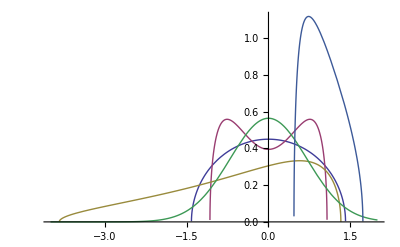

```mathematica
Plot[{emA[x],emB[x],emC[x],G[x]//Re,MP[x]},{x,-4,2}]
```

## Square Root FreePlus Examples

Free probability add A with itself.  Returns another function of the form  SingFun[fun,{1/2,1/2}]

```mathematica
AA=emA~FreePlus~emA;
```

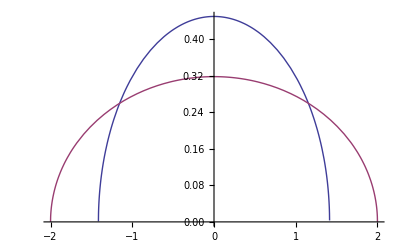

```mathematica
Plot[{emA[x],AA[x]},{x,-2,2}]
```

We can check the RTransforms agree

```mathematica
RTransform[AA,.1 I]-2RTransform[emA,.1 I]
```

-1.11022×10^-16+5.32907×10^-15 ⅈ

We can compare against the histogram:

Free probability add A and B (don’t worry about the warnings)

```mathematica
AB=emA~FreePlus~emB;
```

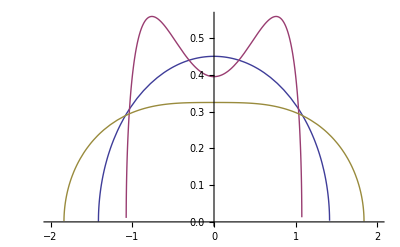

```mathematica
Plot[{emA[x],emB[x],AB[x]},{x,-2,2}]
```

We can check the RTransforms agree

```mathematica
RTransform[AB,.1 I]-(RTransform[emA,.1 I]+RTransform[emB,.1 I])
```

7.71491×10^-14-1.66978×10^-13 ⅈ

Free probability add A and C

```mathematica
AC=emA~FreePlus~emC;
```

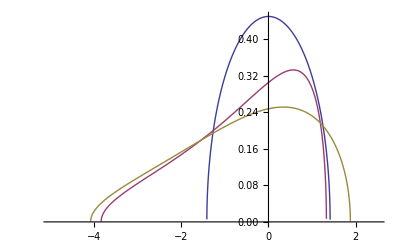

```mathematica
Plot[{emA[x],emC[x],AC[x]},{x,-5,2.5}]
```

We can check the RTransforms agree

```mathematica
RTransform[AC,.1 I]-(RTransform[emA,.1 I]+RTransform[emC,.1 I])
```

2.71005×10^-13-1.9007×10^-13 ⅈ

We can add the semi circle to Marchenko–Pastur distribution

```mathematica
AMP=emA~FreePlus~MP;
```

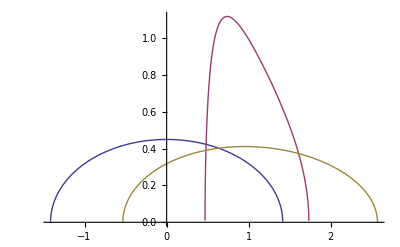

```mathematica
Plot[{emA[x],MP[x],AMP[x]},{x,-2.,3.},PlotRange->All]
```

### Histograms

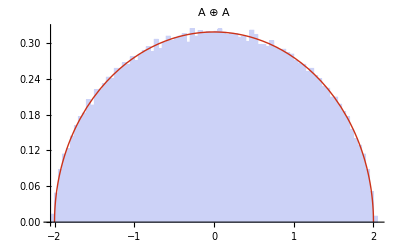

```mathematica
n=300;
HistogramPlot[(
A=RandomSymmetric[n];
B=RandomSymmetric[n];
A+B)&,AA,PlotLabel->"A ⊕ A"]
```

Here we verify the Marchenko–Pastur distribution

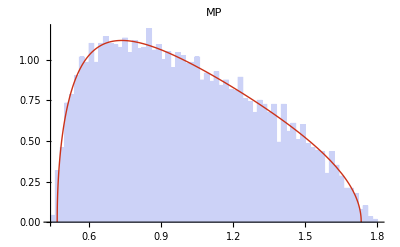

```mathematica
m=70;n=10 m;
HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
A.Transpose[A]/(10 m))&,MP,PlotLabel->"MP"]
```

Here we verify the free addition of a  Marchenko–Pastur distribution with a semicircle

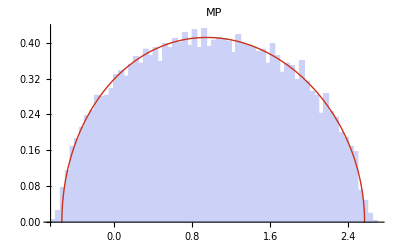

```mathematica
m=70;n=10 m;
HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
B=RandomSymmetric[m];
A.Transpose[A]+B)&,AMP,PlotLabel->"MP"]
```

## Gaussian FreePlus Examples

Gaussian examples (limited sample points means the accuracy won’t be quite as high here).  FreeAddRealLine means we assume the added measure is supported on the real line

```mathematica
GG=emG~FreePlus~emG;
```

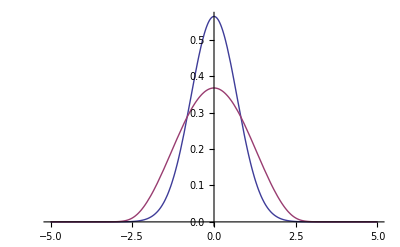

```mathematica
Plot[{emG[x]//Re,GG[x]//Re}//Evaluate,{x,-5,5.}]
```

```mathematica
RTransform[GG,.1 I]-(RTransform[emG,.1 I]+RTransform[emG,.1 I])
```

0.00034914+0.000068117 ⅈ

```mathematica
AG=emA~FreePlus~emG;
```

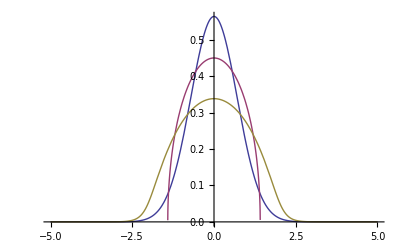

```mathematica
Plot[{emG[x]//Re,emA[x],AG[x]//Re},{x,-5,5.}]
```

```mathematica
BG=emB~FreePlus~emG;
```

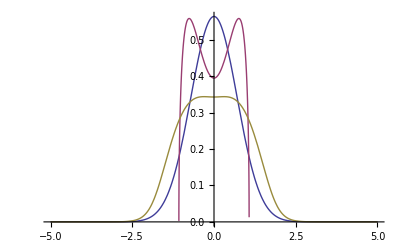

```mathematica
Plot[{emG[x]//Re,emB[x],BG[x]//Re},{x,-5,5.}]
```

Finally, an example where the routine doesn’t work!

```mathematica
CG=emC~FreePlus~emG;
```

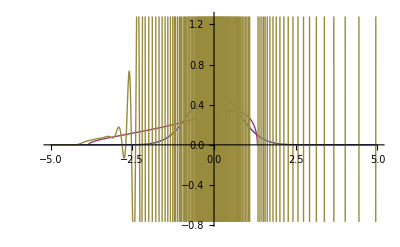

```mathematica
Plot[{emG[x]//Re,emC[x],CG[x]//Re},{x,-5,5.}]
```

### Histograms

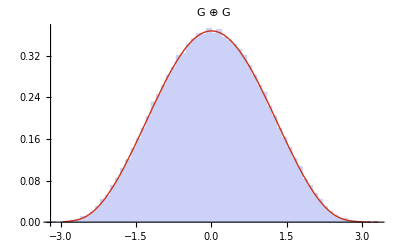

```mathematica
n=300;
HistogramPlot[(
Q=RandomOrthogonal[n];
A=Q.DiagonalMatrix[RandomVariate[NormalDistribution[0,1/Sqrt[2]],n]].Transpose[Q];
Q=RandomOrthogonal[n];
B=Q.DiagonalMatrix[RandomVariate[NormalDistribution[0,1/Sqrt[2]],n]].Transpose[Q];
A+B)&,GG,PlotLabel->"G ⊕ G"]
```

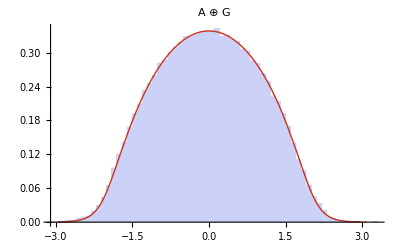

```mathematica
n=300;
HistogramPlot[(
A=RandomSymmetric[n];
Q=RandomOrthogonal[n];
B=Q.DiagonalMatrix[RandomVariate[NormalDistribution[0,1/Sqrt[2]],n]].Transpose[Q];
A+B)&,AG,PlotLabel->"A ⊕ G"]
```

## Finite n FreePlus Examples

We construct a counting measure which approximates the semicircle

```mathematica
n=50;An=PFun[{1/n},Point[#]]&/@(RandomSymmetric[n]//Eigenvalues);
```

There Stieljes transforms are close:

```mathematica
Stieljes[An,1. I]-Stieljes[emA,1.I]
```

0.00215216+0.00322585 ⅈ

We construct an approximation of the Stieljes function on an ellipse:

```mathematica
EAn=LFun[1/(-2π I)Stieljes[An,#]&,Ellipse[{-Sqrt[2],Sqrt[2]},.8 ],150];
```

It’s Stieljestransform is identical to An:

```mathematica
Stieljes[An,1. I]-Stieljes[EAn,1. I]
```

2.75387×10^-16-3.33067×10^-16 ⅈ

## FreeTimes Examples

We need a  measure supported on the positive real line.  Here we shift the semi circle

```mathematica
VS[x_]:=(x-3)^2;
vfS=SingFun[Fun[VS',VS//EquilibriumMeasureSupport//Line],{0,0}];
emS=(-1/(2 π) vfS//HilbertInverse);
```

```mathematica
SxS=emS~FreeTimes~emS;
```

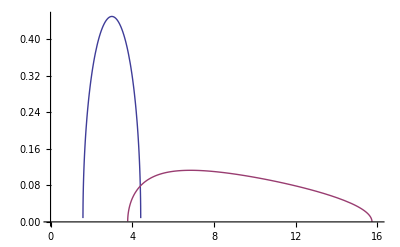

```mathematica
Plot[{emS[x],SxS[x]},{x,0,16}]
```

```mathematica
SxMP=emS~FreeTimes~MP;
```

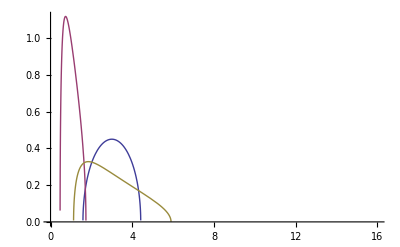

```mathematica
Plot[{emS[x],MP[x],SxMP[x]},{x,0,16}]
```

### Histograms

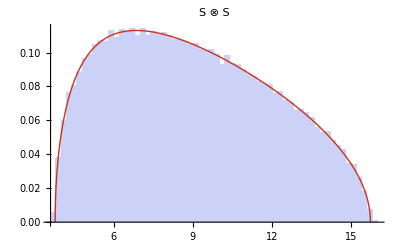

```mathematica
n=300;
HistogramPlot[(
A2=RandomSymmetric[n]+3 IdentityMatrix[n];
A=MatrixPower[A2,1/2];
B=RandomSymmetric[n]+3 IdentityMatrix[n];
A.B.A)&,SxS,PlotLabel->"S ⊗ S"]
```

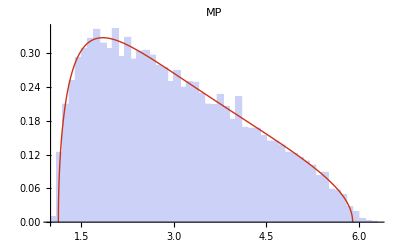

```mathematica
m=70;n=10 m;
HistogramPlot[(
A2=RandomSymmetric[m]+3 IdentityMatrix[m];
A=MatrixPower[A2,1/2];
B=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
A.B.Transpose[B].A)&,SxMP,PlotLabel->"MP"]
```

## FreeCompress Examples

```mathematica
comA2=FreeCompress[emA,.2];
comA4=FreeCompress[emA,.4];
comA8=FreeCompress[emA,.8];
```

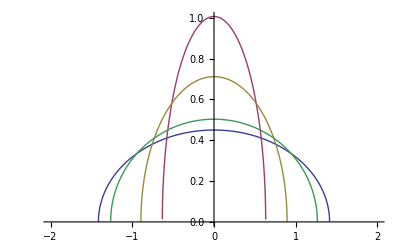

```mathematica
Plot[{emA[x],comA2[x],comA4[x],comA8[x]},{x,-2,2}]
```

```mathematica
comB2=FreeCompress[emB,.2];
comB4=FreeCompress[emB,.4];
comB8=FreeCompress[emB,.8];
```

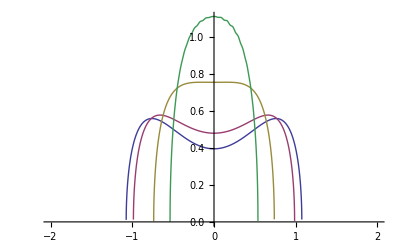

```mathematica
Plot[{emB[x],comB8[x],comB4[x],comB2[x]},{x,-2,2}]
```

```mathematica
comC2=FreeCompress[emC,.2];
comC4=FreeCompress[emC,.4];
comC8=FreeCompress[emC,.8];
```

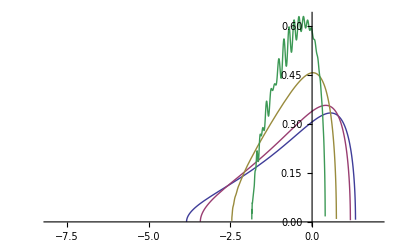

```mathematica
Plot[{emC[x],comC8[x],comC4[x],comC2[x]},{x,-8,2}]
```

Now for the Gaussian example.

```mathematica
comG2=FreeCompress[emG,.2];
comG4=FreeCompress[emG,.4];
comG8=FreeCompress[emG,.8];
```

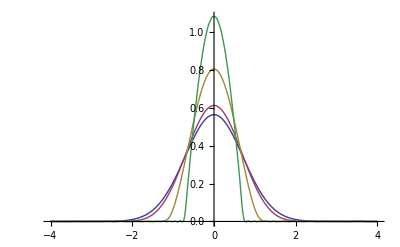

```mathematica
Plot[{emG[x]//Re,comG8[x]//Re,comG4[x]//Re,comG2[x]//Re}//Evaluate,{x,-4,4}]
```

### Histograms

We can compare with histograms

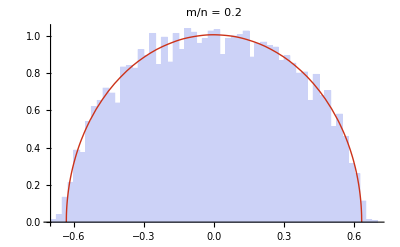

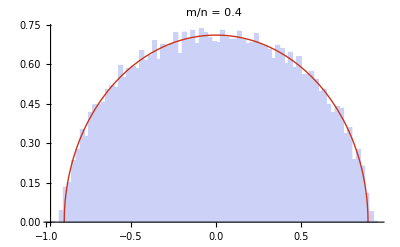

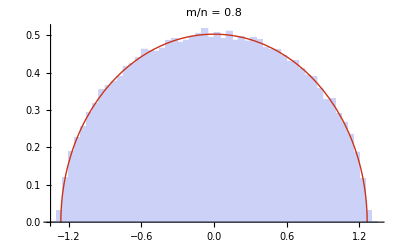

```mathematica
n=300;
m=2/10 n;
HistogramPlot[(Q=RandomOrthogonal[n];
(Q.RandomSymmetric[n].Transpose[Q])⟦;;m,;;m⟧)&,comA2,PlotLabel->"m/n = "<>ToString[m/n//N]]//Print;

m=4/10 n;
HistogramPlot[(Q=RandomOrthogonal[n];
(Q.RandomSymmetric[n].Transpose[Q])⟦;;m,;;m⟧)&,comA4,PlotLabel->"m/n = "<>ToString[m/n//N]]//Print;

n=300;
m=8/10 n;
HistogramPlot[(Q=RandomOrthogonal[n];
(Q.RandomSymmetric[n].Transpose[Q])⟦;;m,;;m⟧)&,comA8,PlotLabel->"m/n = "<>ToString[m/n//N]]//Print;
```